NB- The data importing, etc assume that you've installed everything in the system-wide directory $BaseDirectory/Applications. If not, you'll need to change the paths in the Import statements.

```mathematica
Needs["MDS`"]
```

A batch of judged similarity for 12 stimuli from Norman EtAl -

@article{Norman:2004,
	Author = {Norman, J Farley and Norman, Hideko F and Clayton, Anna Marie and Lianekhammy, Joann and Zielke, Gina},
	Journal = {Percept Psychophys},
	Number = {2},
	Pages = {342--351},
	Title = {The visual and haptic perception of natural object shape.},
	Volume = {66},
	Year = {2004}}

```mathematica
data=Import[ToFileName[{$BaseDirectory,"Applications","MDS","Examples"},"norman.csv"]];
```

```mathematica
MatrixForm[data]
```

(177 | 4 | 76 | 32 | 8 | 0 | 42 | 26 | 1 | 14 | 1 | 16
17 | 357 | 24 | 11 | 0 | 20 | 62 | 28 | 42 | 3 | 23 | 0
162 | 16 | 284 | 67 | 2 | 1 | 95 | 114 | 1 | 18 | 1 | 14
16 | 0 | 11 | 240 | 11 | 0 | 3 | 12 | 0 | 5 | 0 | 15
1 | 0 | 0 | 8 | 386 | 0 | 2 | 3 | 0 | 16 | 0 | 47
0 | 41 | 0 | 3 | 0 | 453 | 1 | 0 | 19 | 0 | 30 | 0
75 | 17 | 41 | 42 | 9 | 1 | 238 | 35 | 6 | 7 | 0 | 1
48 | 1 | 61 | 72 | 15 | 0 | 43 | 256 | 3 | 13 | 0 | 24
1 | 17 | 0 | 2 | 4 | 4 | 8 | 19 | 370 | 20 | 5 | 2
3 | 0 | 2 | 7 | 25 | 0 | 1 | 3 | 3 | 400 | 0 | 37
0 | 47 | 0 | 2 | 1 | 21 | 4 | 1 | 55 | 0 | 440 | 3
0 | 0 | 1 | 14 | 39 | 0 | 1 | 3 | 0 | 4 | 0 | 341)

Here are the unnormalized dissimilarity ratings - we take the reciprocal of the similarity judgements + 1 to avoid division by zero.

```mathematica
dissim=(1.0/(data+1));
```

```mathematica
MatrixForm[dissim]
```

(0.00561798 | 0.2 | 0.012987 | 0.030303 | 0.111111 | 1. | 0.0232558 | 0.037037 | 0.5 | 0.0666667 | 0.5 | 0.0588235
0.0555556 | 0.0027933 | 0.04 | 0.0833333 | 1. | 0.047619 | 0.015873 | 0.0344828 | 0.0232558 | 0.25 | 0.0416667 | 1.
0.00613497 | 0.0588235 | 0.00350877 | 0.0147059 | 0.333333 | 0.5 | 0.0104167 | 0.00869565 | 0.5 | 0.0526316 | 0.5 | 0.0666667
0.0588235 | 1. | 0.0833333 | 0.00414938 | 0.0833333 | 1. | 0.25 | 0.0769231 | 1. | 0.166667 | 1. | 0.0625
0.5 | 1. | 1. | 0.111111 | 0.00258398 | 1. | 0.333333 | 0.25 | 1. | 0.0588235 | 1. | 0.0208333
1. | 0.0238095 | 1. | 0.25 | 1. | 0.00220264 | 0.5 | 1. | 0.05 | 1. | 0.0322581 | 1.
0.0131579 | 0.0555556 | 0.0238095 | 0.0232558 | 0.1 | 0.5 | 0.0041841 | 0.0277778 | 0.142857 | 0.125 | 1. | 0.5
0.0204082 | 0.5 | 0.016129 | 0.0136986 | 0.0625 | 1. | 0.0227273 | 0.00389105 | 0.25 | 0.0714286 | 1. | 0.04
0.5 | 0.0555556 | 1. | 0.333333 | 0.2 | 0.2 | 0.111111 | 0.05 | 0.00269542 | 0.047619 | 0.166667 | 0.333333
0.25 | 1. | 0.333333 | 0.125 | 0.0384615 | 1. | 0.5 | 0.25 | 0.25 | 0.00249377 | 1. | 0.0263158
1. | 0.0208333 | 1. | 0.333333 | 0.5 | 0.0454545 | 0.2 | 0.5 | 0.0178571 | 1. | 0.00226757 | 0.25
1. | 1. | 0.5 | 0.0666667 | 0.025 | 1. | 0.5 | 0.25 | 1. | 0.2 | 1. | 0.00292398)

This creates a datastructure stored in 'm' that is operated on by the iteration routines

```mathematica
m=MultidimensionalScaling[dissim,2];
```

m[[1]] contains the configuration of the stimuli, m[[2]] and m[[3]] contain the state data (SVDd data) and m[[4]] contains the current stress. We're requesting a 2-D solution.

So, here we'll iterate the MDS nIterations times, accumulate the state in the list 'mds', and when we're done, plot the stress over all iterations...

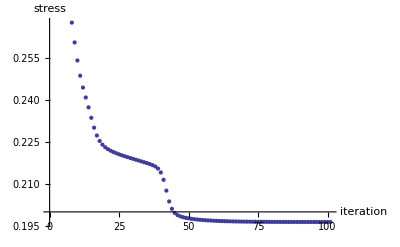

```mathematica
mds={m};
nIterations=100;
Do[AppendTo[mds,m=IterateMDS[m]],{nIterations}];
ListPlot[mds⟦All,4⟧,AxesLabel->{"iteration","stress"}]
```

Here's another way to do it with fixedpointlist

```mathematica
m=MultidimensionalScaling[dissim,2];
maxIters=1000;
mds=FixedPointList[IterateMDS,m,maxIters,SameTest->(Abs[#1⟦4⟧-#2⟦4⟧]<1*^-6&)];
```

See, here it only took 96 iterations to converge within 1/1000000

```mathematica
nIterations=Length[mds]
```

96

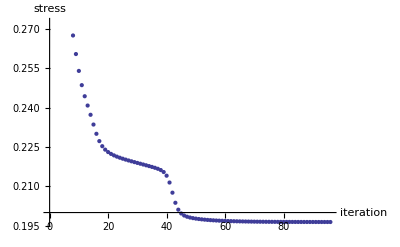

```mathematica
ListPlot[mds⟦All,4⟧,AxesLabel->{"iteration","stress"}]
```

final confuiguration is the first element in the last element of 'mds'

```mathematica
finalConf=First[Last[mds]]
```

{{1.01912,1.26289},{-0.836092,1.58848},{1.44699,0.918625},{1.6031,-0.27367},{0.776121,-1.87681},{-2.24411,1.18246},{0.129473,0.760921},{0.5388,-0.248985},{-1.34184,0.0267364},{1.24995,-1.13297},{-2.34218,-0.195547},{0.000680254,-2.01213}}

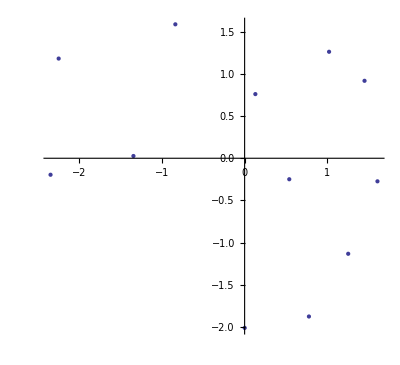

```mathematica
ListPlot[finalConf,AspectRatio->Automatic]
```

Here - with a little style

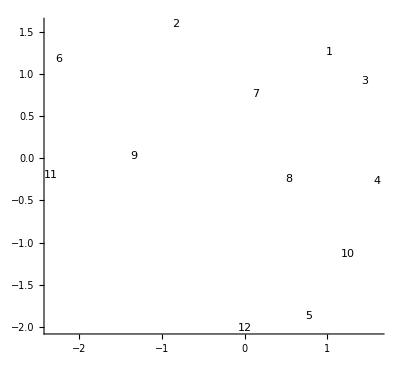

```mathematica
Show[Graphics[MapThread[
Text[Style[#1,"Title"],#2]&,{ ToString/@ Range[12],finalConf}]],Axes->True]
```

```mathematica
a=Animate[Show[Graphics[MapThread[
Text[Style[#1,"Title"],#2]&,{ ToString/@ Range[12],First[mds[[t]]]}]],Axes->True,PlotRange->{{-3,3},{-3,3}}],{t,1,nIterations,1}]
```

```mathematica
images=Import/@Table[ToFileName[{$BaseDirectory,"Applications","MDS","Examples","Images"},ToString[i]<>".png"],{i,1,12}];
```

If you'd like to see them-

```mathematica
GraphicsGrid[Partition[images,3],ImageSize->{400,Automatic}]
```

And here is a plot of them, sans axis, etc, of the final configuration-

```mathematica
Show[Graphics[MapThread[
Translate[images[[#1]][[1]],#2*400]&,{ Range[12],finalConf}]],Axes->False]
```

-Graphics-